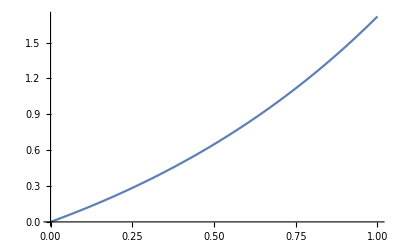
{0.276,-Graphics-}

```mathematica
Plot[Sum[x^k/(k!),{k,1,1000}],{x,0,1},DisplayFunction->Identity]//Timing
```

```mathematica
Plot[Evaluate[Sum[x^k/(k!),{k,1,1000}]],{x,0,1},DisplayFunction->Identity]//Timing
```

{0.192,-Graphics-}

```mathematica
Clear[a,b];
a=b;Evaluate[a]=2;
{OwnValues[a],OwnValues[b]}
```

{{HoldPattern[a]:>b},{HoldPattern[b]:>2}}

```mathematica
c=2;
```

```mathematica
OwnValues[c]
```

{HoldPattern[c]:>2}

```mathematica
d:=2;
```

```mathematica
OwnValues[d]
```

{HoldPattern[d]:>2}

```mathematica
f[x_]=x;
```

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>x}

```mathematica
f[x_]:=x;
```

```mathematica
DownValues[f]
```

{HoldPattern[f[x_]]:>x}

```mathematica
f[Evaluate[1+1]]
```

2

```mathematica
Hold[f[Evaluate[1+1]]]
```

Hold[f[Evaluate[1+1]]]